```mathematica
Solve[Q == α (1-m)^2 + (1-α)Q (1-m)^2,Q]
Qe=Q/.%⟦1⟧//FullSimplify
Qe/.α->1/n//FullSimplify
```

{{Q→((-1+m)^2 α)/(2 m-m^2+α-2 m α+m^2 α)}}

((-1+m)^2 α)/((-2+m) m (-1+α)+α)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

```mathematica
W = -c - (b-c)(1-m)^2/n+Q*(b-(b-c)(n-1)(1-m)^2/n);
Collect[W, b,FullSimplify]
```

(c (1-2 m+m^2-n+(-1+m)^2 (-1+n) Q))/n+(b (-1+Q-(-2+m) m (1+(-1+n) Q)))/n

```mathematica
κ=(-1+Q-(-2+m) m (1+(-1+n) Q))/n/(-(1-2 m+m^2-n+(-1+m)^2 (-1+n) Q)/n)//FullSimplify
```

(1-Q+(-2+m) m (1+(-1+n) Q))/(1-2 m+m^2-n+(-1+m)^2 (-1+n) Q)

```mathematica
WW=W/.Q->Qe//FullSimplify
WW/.α->1/n//FullSimplify
```

-c-((b-c) (-1+m)^2)/n+((-1+m)^2 (b-((b-c) (-1+m)^2 (-1+n))/n) α)/((-2+m) m (-1+α)+α)

-(c (-2+m) m n)/(-1+(-2+m) m (-1+n))

```mathematica
(-c (2-m) m n)/(1+(2-m) m (n-1)) - (-(c (-2+m) m n)/(-1+(-2+m) m (-1+n)))//FullSimplify
```

0

```mathematica
WW/.n->4/.α->1/2//FullSimplify
```

((-2+m) m (b (-1+m)^2-c (5+(-2+m) m)))/(2 (-1+(-2+m) m))

```mathematica
M1=(ND-1)/(1-((1-μ)^2(ND(1-m)-1)^2)/(ND-1)^2); M2=1/(1-(1-μ)^2);
QWF=(-ND+M1+M2)/((n-1)ND+M1+M2);
Limit[QWF,ND->∞]
QWF0=Limit[%,μ->0]//FullSimplify
```

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2-2 (-1+n) μ+(-1+n) μ^2)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

```mathematica
κ/.Q->QWF0//FullSimplify
```

0

```mathematica
κ/.Q->Qe//FullSimplify
```

((-1+m)^2 (-1+n α))/(-1+n+n α+(-2+m) m (-1+n α))

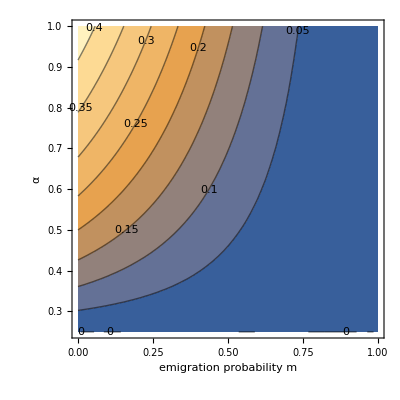

```mathematica
myn =4;
ContourPlot[κ/.Q->Qe/.n->myn,{m,0.00001,1},{α,1/myn,1},ContourLabels->True,FrameLabel->{"emigration probability m", "α"}]
```